```mathematica
u090494e　荒井直幸　2014年10月28日
```

Sin[x]

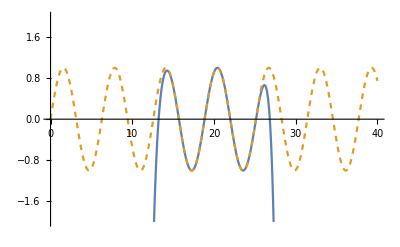

```mathematica
taylor=Normal[Series[Sin[x],{x,20,15}]];
ss=Sin[x]
Plot[{taylor,ss},{x,0,40},PlotRange->{-2,2},PlotStyle->{{},Dashing[{0.01}]}]
```

```mathematica
ArcTan[1]
ArcSin[1]
ArcCos[1]
```

π/4

π/2

0

```mathematica
taylor1=Normal[Series[ArcTan[x],{x,0,1000}]];
4 N[taylor1/.x->1]
```

3.13959

```mathematica
課題１
```

```mathematica
N[ArcTan[1/2]]
N[ArcTan[1/3]]
4 (N[ArcTan[1/2]]+N[ArcTan[1/3]])
taylor2=Normal[Series[ArcTan[x],{x,0,14}]];
taylor201=4 N[taylor2/.x->1/2]
taylor3=Normal[Series[ArcTan[x],{x,0,14}]];
taylor301=4 N[taylor3/.x->1/3]
taylor201+taylor301
taylor4=Normal[Series[ArcTan[x],{x,0,15}]];
taylor401=4 N[taylor4/.x->1/2]
taylor5=Normal[Series[ArcTan[x],{x,0,15}]];
taylor501=4 N[taylor5/.x->1/3]
taylor401+taylor501
```

0.463648

0.321751

3.14159

1.8546

1.287

3.1416

1.85459

1.287

3.14159

```mathematica
よって１５次
```

```mathematica
課題２
```

```mathematica
taylor4=Normal[Series[Exp[x],{x,0,7}]];
N[taylor4/.x->1]
taylor4=Normal[Series[Exp[x],{x,0,8}]];
N[taylor4/.x->1]
```

2.71825

2.71828

```mathematica
よって８次
```

-7.67368+3.77368 x

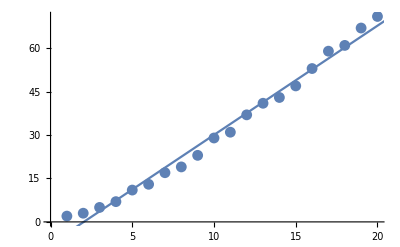

```mathematica
tab1=Table[Prime[x],{x,20}];
plot1=ListPlot[tab1];
fit1=Fit[tab1,{1,x},x]
plot2=Plot[fit1,{x,0,21}];
Show[plot1,plot2]
```

-1.92368+2.2055 x+0.0746753 x^2

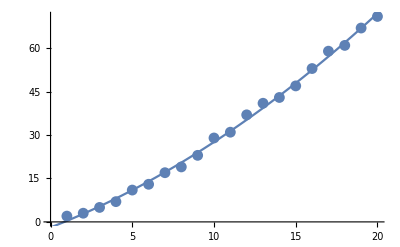

```mathematica
fit2=Fit[tab1,{1,x,x^2},x]
plot3=Plot[fit2,{x,0,21}];
Show[plot1,plot3]
```

0.160784+1.14189 x+0.19826 x^2-0.00392334 x^3

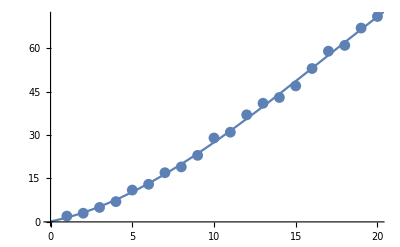

```mathematica
fit3=Fit[tab1,{1,x,x^2,x^3},x]
plot4=Plot[fit3,{x,0,21}];
Show[plot1,plot4]
```

```mathematica
課題３のa
```

109679.-109679. x

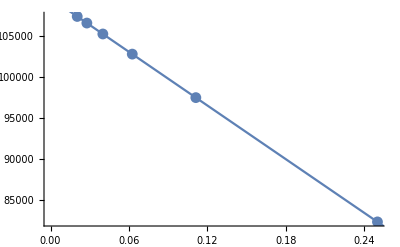

```mathematica
wave1={{1/2^2,82259},{1/3^2,97492},{1/4^2,102824},{1/5^2,105292},{1/6^2,106632},{1/7^2,107440}};
plot5=ListPlot[wave1];
fit4=Fit[wave1,{1,x},x]
plot6=Plot[fit4,{x,0,1}];
Show[plot5,plot6]
```

```mathematica
リュードベリ定数はこのグラフの切片の値なので
```

```mathematica
109679　[cm^-1]
```

```mathematica
イオン化エネルギーは
```

```mathematica
6.62607*10^-34*2.99792458*10^8*100*109679*6.02214*10^23*4.184
```

5.48963×10^6

```mathematica
よって
```

```mathematica
5490　[kcal mol^-1]
```

```mathematica
課題３のb
```

```mathematica
wave2={{320},{330},{345},{360},{385}};
2.9979246*10^10*10^7/wave2
wave3={{1.17},{1.05},{0.885},{0.735},{0.511}}*1.602177*10^(-12)
```

{{9.36851×10^14},{9.08462×10^14},{8.68964×10^14},{8.32757×10^14},{7.78682×10^14}}

{{1.87455×10^-12},{1.68229×10^-12},{1.41793×10^-12},{1.1776×10^-12},{8.18712×10^-13}}

-4.37731×10^-12+6.67119×10^-27 x

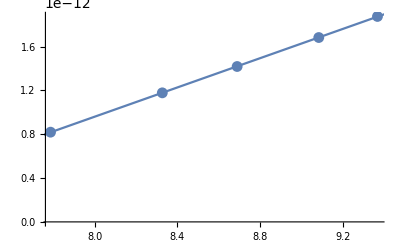

```mathematica
wave4={{9.368514375*10^14,1.874547089999999*10^-12},{9.0846*10^14,1.682285850000000*10^-12},{8.6896365217391*10^14,1.417926645*10^-12},{8.32756833333333*10^14,1.17760009*10^-12},{7.78681714285714*10^14,8.1871244*10^-13}};
plot7=ListPlot[wave4];
fit5=Fit[wave4,{1,x},x]
plot8=Plot[fit5,{x,0,10^15}];
Show[plot7,plot8]
```

```mathematica
プランク定数はグラフの傾きなので
```

```mathematica
6.671*10^-34　[J s]
```

```mathematica
仕事関数はグラフの切片なので
```

```mathematica
-4.377*10^-12　[J]
```